Sapphire
Q^-1vsb

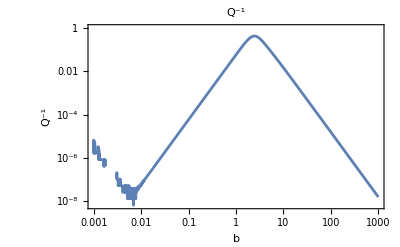

```mathematica
QwoHeatFlow =δE Abs[ 6/(2ξ)^2-6/(2ξ)^3(Sinh[2ξ]+Sin[2ξ])/(Cosh[2ξ]+Cos[2ξ]) ]/.
{δE->0.88,ξ->0.29 b^(3/2)};
QHeatFlowg=LogLogPlot[QwoHeatFlow,{b,0.001,1000},PlotLabel->"Q^-1", Frame->True,FrameLabel->{b,"Q^-1"}]
```

```mathematica
QHeatFlow=δE Abs[3/(4 ξ^3)-1/(Cos[2 d ξ]+Cosh[2 d ξ])(Cos[ξ(d-1)]Sinh[ξ(d+1)]+Cos[ξ(d+1)]Sinh[ξ(1-d)]-Sin[ξ(d-1)]Cosh[ξ(1+d)]+Sin[ξ(1+d)]Cosh[ξ(1-d)]-2ξ(Cos[ξ(d-1)]Cosh[ξ(1+d)]+Cos[ξ(d+1)]Cosh[ξ(1-d)]))]/.{δE->0.88,ξ->0.29 b^(3/2)}; (*sapphire*)
```

d=1.1,1.3,1.7

27.0614 Abs[1/(b^(9/2) (Cos[0.638 b^(3/2)]+Cosh[0.638 b^(3/2)]))(-0.58 b^(3/2) (Cos[0.609 b^(3/2)] Cosh[0.029 b^(3/2)]+Cos[0.029 b^(3/2)] Cosh[0.609 b^(3/2)])-Cosh[0.609 b^(3/2)] Sin[0.029 b^(3/2)]+Cosh[0.029 b^(3/2)] Sin[0.609 b^(3/2)]-Cos[0.609 b^(3/2)] Sinh[0.029 b^(3/2)]+Cos[0.029 b^(3/2)] Sinh[0.609 b^(3/2)])]

27.0614 Abs[1/(b^(9/2) (Cos[0.754 b^(3/2)]+Cosh[0.754 b^(3/2)]))(-0.58 b^(3/2) (Cos[0.667 b^(3/2)] Cosh[0.087 b^(3/2)]+Cos[0.087 b^(3/2)] Cosh[0.667 b^(3/2)])-Cosh[0.667 b^(3/2)] Sin[0.087 b^(3/2)]+Cosh[0.087 b^(3/2)] Sin[0.667 b^(3/2)]-Cos[0.667 b^(3/2)] Sinh[0.087 b^(3/2)]+Cos[0.087 b^(3/2)] Sinh[0.667 b^(3/2)])]

27.0614 Abs[1/(b^(9/2) (Cos[0.986 b^(3/2)]+Cosh[0.986 b^(3/2)]))(-0.58 b^(3/2) (Cos[0.783 b^(3/2)] Cosh[0.203 b^(3/2)]+Cos[0.203 b^(3/2)] Cosh[0.783 b^(3/2)])-Cosh[0.783 b^(3/2)] Sin[0.203 b^(3/2)]+Cosh[0.203 b^(3/2)] Sin[0.783 b^(3/2)]-Cos[0.783 b^(3/2)] Sinh[0.203 b^(3/2)]+Cos[0.203 b^(3/2)] Sinh[0.783 b^(3/2)])]

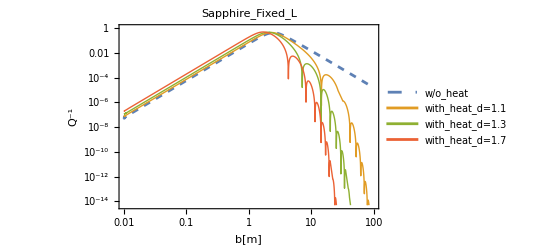

```mathematica
Q11=QHeatFlow/.{d->1.1}
Q13=QHeatFlow/.{d->1.3}
Q17=QHeatFlow/.{d->1.7}
HeatFlowg=LogLogPlot[{QwoHeatFlow,Q11,Q13,Q17},{b,0.01,100},PlotLabel->"Sapphire_Fixed_L", Frame->True,FrameLabel->{"b[m]","Q^-1"},PlotLegends->Placed[{"w/o_heat","with_heat_d=1.1","with_heat_d=1.3","with_heat_d=1.7"},{0.3,0.25}],GridLinesStyle->LightGray,GridLines->Full,PlotStyle->{Dashed,Thick,Thick,Thick}]
```